# A338920 - draft notes

### Initial Commit

Name:
	
Number of times it takes to reduce n to its smallest possible value, equal or larger than zero, by removing leading digit of n, while the decatenated value of n is smaller than n and not equal to zero.

a(n) = while n is larger or equal to zero; n - leading digit of n removed, while n is smaller than n and not equal to zero.

Data: 
	
0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 11, 6, 4, 3, 3, 2, 2, 2, 2, 0, 21, 11, 7, 6, 5, 4, 3, 3, 3, 0, 31, 16, 11, 8, 7, 6, 5, 4, 4, 0, 41, 21, 14, 11, 9, 7, 6, 6, 5, 0, 51, 26, 17, 13, 11, 9, 8, 7, 6, 0, 61, 31, 21, 16, 13, 11, 9, 8, 7, 0, 71, 36, 24, 18, 15, 12, 11, 9

0,0,0,0,0,0,0,0,0,0,11,6,4,3,3,2,2,2,2,0,21,11,7,6,5,4,3,3,3,0,31,16,11,8,7,6,5,4,4,0,41,21,14,11,9,7,6,6,5,0,51,26,17,13,11,9,8,7,6,0,61,31,21,16,13,11,9,8,7,0,71,36,24,18,15,12,11,9,8,0,81,41,27,21,17,14,12,11,9,0,91,46,31,23,19,16,13,12,11,0

Example: 

For n = 121 the a(121) = 21 since it takes 21 time to reduce 121 to the smallest possible digit.
121-21-21-21-21-21-1-1-1-1-1-1-1-1-1-1-1-1-1-1-1-1 = subtracted 21 times.

Crossrefs:
	
Cf. A062028, A007953, A047791, A107743.

### Formula

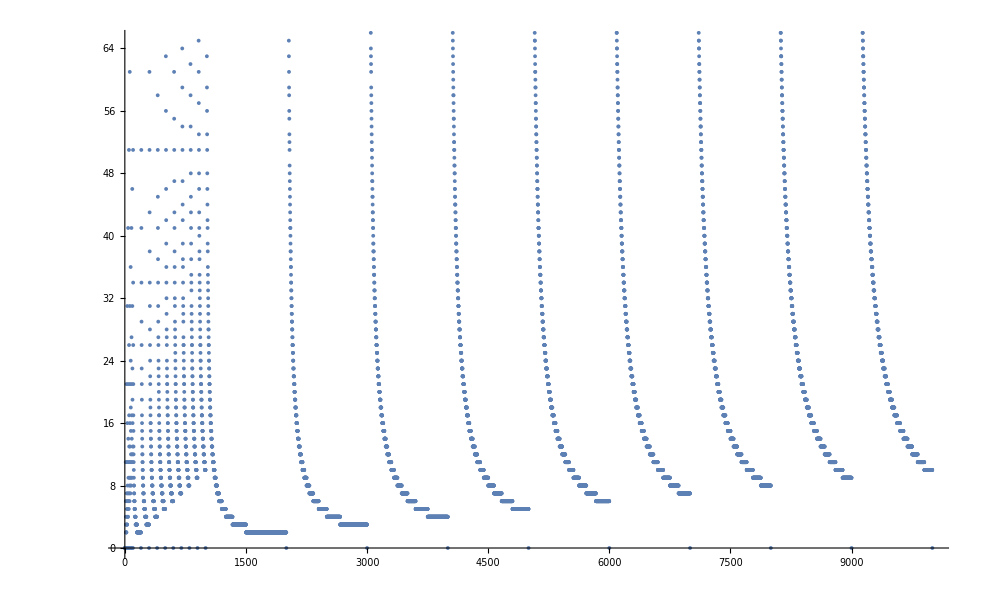

```mathematica
count=10000;SubCount={};
Do[(n=m=k;c=0;
While[n>0,If[n≤m,m=ToExpression[StringDrop[ToString[k],1]],m];
If[m==Null || m==0,Break[]];n-=m;
If[n<0,Break[]];c++;
];AppendTo[SubCount,c];),{k,1,count,1}];
ListPlot[SubCount]

(*Print[SubCount];*)
```